### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np=4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3, x4}
xpcoord = {x1p,x2p,x3p, x4p}
```

-1<k&&Im[k]==0

{x1,x2,x3,x4}

{x1p,x2p,x3p,x4p}

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

### Defining Exponential Functions, Normalization and HF Basis Functions

```mathematica
(*efunN denote the exponential functions for the N-particle reduced densitry operator and efun..poly defines the polynomial of the exponential*)
```

```mathematica
efun4[a_,b_, x1_, x2_, x3_, x4_]:=Exp[-a(x1^2+x2^2+x3^2+x4^2)+b(x1+x2+x3+x4)^2];
```

```mathematica
efun3[a_,b_, x1_, x2_, x3_, x1p_, x2p_, x3p_]:=ⅇ^(-(b^2 (x1-x1p+x2-x2p+x3-x3p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (x1^2+x1p^2+x2^2+x2p^2+x2 x3+x3^2+x1 (x2+x3)+x2p x3p+x3p^2+x1p (x2p+x3p)))/(2 (a-b)))
```

```mathematica
efun4poly[a_,b_, x1_, x2_, x3_, x4_]:=-a(x1^2+x2^2+x3^2+x4^2)+b(x1+x2+x3+x4)^2;
efun3poly[a_,b_]:=-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p+x3-x3p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2)-4 a b (x1^2+x1p^2+x2^2+x2p^2+x2 x3+x3^2+x1 (x2+x3)+x2p x3p+x3p^2+x1p (x2p+x3p)));
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
efunana2rdo[a_,b_,Np_, x1_, x1p_, x2_, x2p_]:=Exp[-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2];
efun2poly[a_,b_, Np_]:=-a(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;
efun1[a_,b_, x1_, x1p_]:=Exp[-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)]*Exp[b^2(Np-1)/(a-b(Np-1)) x1* x1p];
efun1poly[a_,b_]:=-(a-b-b^2(Np-1)/(2(a-b(Np-1))))(x1^2+x1p^2)+(b^2(Np-1)/(a-b(Np-1)) x1* x1p)
```

```mathematica
(*Integrate[efun3[a,b, x1, x2, x3]*efun3[a,b,x1,x2,x3],{x1,-∞,+∞},{x2,-∞,+∞},{x3,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efun1[a,b,x1,x1],{x1,-∞,+∞}, Assumptions-> a>0 && b<0 ]*)
```

```mathematica
(*Integrate[efunana2rdo[a,b,Np,x1,x1, x2, x2],{x1,-∞,+∞}, {x2,-∞,+∞},Assumptions-> a>0 && Im[a]==Im[b]==0]*)
```

```mathematica
(*Integrate[efun1rdo[a,b, x1,x1, x2, x2, Np],{x1,-∞,+∞}, {x2,-∞,+∞}, Assumptions-> a>0 && b<0 && Np∈PositiveIntegers ]*)
```

```mathematica
(*norm /normpre denotes the normalization of the N-particle RDO with respect to the intrinisc length scales lm, lp or the constants A/B*)
norm4rdopre[a_,b_, Np_]:=(π^2/(4 a √(a (a-4 b))))^(-1);
norm4rdo[lm_,lp_, Np_]:=norm4rdopre[A[lp],B[lm,lp, Np], Np];
norm2rdopre[a_,b_, Np_]:=(π/(2 √((a (a-4 b))/(a-3 b)) √((a (a-3 b))/(a-2 b))))^(-1);
norm2rdo[lm_,lp_, Np_]:=norm2rdopre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
norm3rdopre[a_,b_, Np_]:=((√((a-b)/(a^3 (a-4 b))) π^(3/2))/(2 √2))^(-1);
norm3rdo[lm_,lp_, Np_]:=norm3rdopre[A[lp],B[lm,lp, Np], Np];
norm1rdopre[a_,b_, Np_]:=(√((a π-3 b π)/(2 a^2-8 a b)))^(-1)
norm1rdo[lm_,lp_, Np_]:=norm1rdopre[A[lp],B[lm,lp, Np], Np];
```

```mathematica
(*define 2 particle hf basis in terms of permanents*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hf2basis[m1_, m2_, n1_,n2_,a_]:=1/2(hfcoef[m1,x1,a]*hfcoef[m2,x2, a]+hfcoef[m2,x1,a]*hfcoef[m1,x2,a])*1/2(hfcoef[n1,x1p,a]*hfcoef[n2,x2p,a]+hfcoef[n2,x1p,a]*hfcoef[n1,x2p,a])
hf3basis[m1_, m2_,m3_, n1_,n2_,n3_,a_]:=1/6*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a]}}]*1/6*Permanent[{{hfcoef[n1,x1p,a], hfcoef[m1,x2p,a], hfcoef[m1,x3p,a]},{hfcoef[m2,x1p,a], hfcoef[m2,x2p,a], hfcoef[m2,x3p,a]},{hfcoef[m3,x1p,a], hfcoef[m3,x2p,a], hfcoef[m3,x3p,a]}}]
hf4basis[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,a_]:=1/24*Permanent[{{hfcoef[m1,x1,a], hfcoef[m1,x2,a], hfcoef[m1,x3,a], hfcoef[m1, x4,a]},{hfcoef[m2,x1,a], hfcoef[m2,x2,a], hfcoef[m2,x3,a], hfcoef[m2,x4,a]},{hfcoef[m3,x1,a], hfcoef[m3,x2,a], hfcoef[m3,x3,a], hfcoef[m3,x4,a]},{hfcoef[m4,x1,a], hfcoef[m4,x2,a], hfcoef[m4,x3,a], hfcoef[m4,x4,a]}}]*1/24*Permanent[{{hfcoef[m1,x1p,a], hfcoef[m1,x2p,a], hfcoef[m1,x3p,a], hfcoef[m1, x4p,a]},{hfcoef[m2,x1p,a], hfcoef[m2,x2p,a], hfcoef[m2,x3p,a], hfcoef[m2,x4p,a]},{hfcoef[m3,x1p,a], hfcoef[m3,x2p,a], hfcoef[m3,x3p,a], hfcoef[m3,x4p,a]},{hfcoef[m4,x1p,a], hfcoef[m4,x2p,a], hfcoef[m4,x3p,a], hfcoef[m4,x4p,a]}}]
hf1basis[m1_, n1_,a_]:=(hfcoef[m1,x1,a]*hfcoef[n1,x1p,a])
```

### Determining the coefficients of the Polynomial Contribution to the integral

```mathematica
(*Determine the coefficients of the polynomial 'hfibasis' by the coefficientlist function where q corresponds to the power, i.e. x^q , importantly this is not the mathematica index, maxdegreestart denotes the largest q in the polynomial with non-zero entries*)
```

```mathematica
coefstart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,x_,q_,a_] :=CoefficientList[hf4basis[m1,m2,m3,m4,n1,n2,n3,n4,a], x][[q+1]]
maxdegreestart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_, x_] := Length[CoefficientList[hf4basis[m1,m2,m3,m4,n1,n2,n3,n4,a], x]]-1
constantstart4[m1_, m2_,m3_,m4_, n1_,n2_,n3_,n4_,x_] := coefstart3[m1,m2,m3,m4,n1,n2,n3,n4,x,1,a]

coefstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_,q_,a_] :=CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x][[q+1]]
maxdegreestart3[m1_, m2_,m3_, n1_,n2_,n3_, x_] := Length[CoefficientList[hf3basis[m1,m2,m3,n1,n2,n3,a], x]]-1
constantstart3[m1_, m2_,m3_, n1_,n2_,n3_,x_] := coefstart3[m1, m2,m3, n1,n2,n3,x,1,a]

coefstart2[m1_, m2_, n1_,n2_,x_,q_,a_] :=CoefficientList[hf2basis[m1,m2,n1,n2,a], x][[q+1]]
maxdegreestart2[m1_,m2_,n1_,n2_, x_] := Length[CoefficientList[hf2basis[m1,m2,n1,n2,a], x]]-1
constantstart2[m1_, m2_, n1_,n2_,x_] := coefstart2[m1, m2, n1,n2,x,1,a]

coefstart1[m1_, n1_,x_,q_,a_] :=CoefficientList[hf1basis[m1,n1,a], x][[q+1]]
maxdegreestart1[m1_,n1_, x_] := Length[CoefficientList[hf1basis[m1,n1,a], x]]-1
constantstart1[m1_, n1_,x_] := coefstart1[m1, n1,x,1,a]
```

```mathematica
(*sanity check that the coefficient decomposition was correctly performed*)
```

```mathematica
Sum[coefstart3[5,5,2,5,4,3,x1,q,a]*x1^q,{q,0,maxdegreestart3[5,5,2,5,4,3,x1]}]-hf3basis[5,5,2,5,4,3,a]//Simplify
```

0

### Integrating coefficient by coefficient and determining helper functions/exponential polynomials

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
(*exppolyinitN is the polynomial of the Exp contribution to the N-particle RDO*)
```

```mathematica
exppolyinit4 = efun4poly[a,b,x1,x2,x3, x4]+efun4poly[a,b,x1p,x2p,x3p, x4p]-a(x1^2+x2^2+x3^2+x4^2+x1p^2+x2p^2+x3p^2+x4p^2)
exppolyinit3 = efun3poly[a,b]-a(x1^2+x2^2+x3^2+x1p^2+x2p^2+x3p^2);
exppolyinit2=-2a*(x1^2+x2^2+x1p^2+x2p^2)+b((x1+x2)^2+(x1p+x2p)^2)+cp[a,b,Np]*(x1+x1p+x2+x2p)^2;
```

b (x1+x2+x3+x4)^2-a (x1^2+x2^2+x3^2+x4^2)+b (x1p+x2p+x3p+x4p)^2-a (x1p^2+x2p^2+x3p^2+x4p^2)-a (x1^2+x1p^2+x2^2+x2p^2+x3^2+x3p^2+x4^2+x4p^2)

```mathematica
exppolyinit1 = efun1poly[a,b]-a(x1^2+x1p^2)
```

(3 b^2 x1 x1p)/(a-3 b)-a (x1^2+x1p^2)+(-a+b+(3 b^2)/(2 (a-3 b))) (x1^2+x1p^2)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
(*sanity check to see whether coefficients have been correctly decomposed*)
exppolyinit3-(Sum[efuncoef[exppolyinit3,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(* the intxmab function is the results of the following integral:
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*, it gives the integral over all space of x^m* Exp[a x^2+b x], where the function inputs correspond to the polynomial power, quadratic and linear exponential coefficient respectively *)
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
(*inxmabpoly returns the polynomial contribution of the integration inxmab*)
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
(*intexppoly defines the remaining part of the exponential function which in "Running the algorithm" consists of all the coefficients in the remaining variables*)
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)
```

```mathematica
(*intNpoly is the initial polynomial used to run the integration algorithm which iteratively applies the intmxab function to all different variables one after the other. x1 has been picked as the first integration variable, intgenpoly takes a subsequently evaluated polynomial poly as input to evaluate the integral with respect to the exppoly expontial and the variable xint*)
```

```mathematica
int4poly[m1_,m2_,m3_,m4_,n1_,n2_,n3_,n4_]:= Sum[coefstart4[m1,m2,m3,m4,n1,n2,n3,n4,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit4, x1, 2], efuncoef[exppolyinit4, x1, 1]], {q,0, maxdegreestart4[m1,m2,m3,m4,n1,n2,n3,n4, x1]}]
int3poly[m1_,m2_,m3_,n1_,n2_,n3_]:= Sum[coefstart3[m1,m2,m3,n1,n2,n3,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]], {q,0, maxdegreestart3[m1,m2,m3,n1,n2,n3, x1]}]
int2poly[m1_,m2_,n1_,n2_]:= Sum[coefstart2[m1,m2,n1,n2,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]], {q,0, maxdegreestart2[m1,m2,n1,n2, x1]}]
int1poly[m1_,n1_]:= Sum[coefstart1[m1,n1,x1, q, a ]*intxmabpoly[q,efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]], {q,0, maxdegreestart1[m1,n1, x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm for the various particle sectors

```mathematica
mode = 3
```

3

```mathematica
(*the algorithm runs recursively,such that polym..i and exppolym...i (m <-> N=1, mm <-> N=2, mmm <-> N=3, mmmm <-> N=4) define the relevant polynomials and exponential functions which arise from integrating in the various variables*)
```

### Run algorithm for 1 RDO

```mathematica
polym1 = int1poly[mode, mode];
exppolym1= efuncoef[exppolyinit1, x1, 0]+ intexppoly[efuncoef[exppolyinit1, x1, 2], efuncoef[exppolyinit1, x1, 1]] // Simplify
```

-(2 a (4 a^2-16 a b+7 b^2) x1p^2)/(4 a^2-14 a b+3 b^2)

```mathematica
polym2 = intgenpoly[polym1, exppolym1, x1p] // Simplify
exppolym2 = efuncoef[exppolym1, x1p, 0]+ intexppoly[efuncoef[exppolym1, x1p, 2], efuncoef[exppolym1, x1p, 1]] // Simplify
```

(9 √a b^4 (2 a^2-8 a b+11 b^2))/(√((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^3 √((4 a^3-16 a^2 b+7 a b^2)/(8 a^2 π-28 a b π+6 b^2 π)))

0

```mathematica
finalanswerm =norm1rdopre[a,b,Np]* polym2*Exp[exppolym2]
```

(9 √a b^4 (2 a^2-8 a b+11 b^2))/(√((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^3 √((a π-3 b π)/(2 a^2-8 a b)) √((4 a^3-16 a^2 b+7 a b^2)/(8 a^2 π-28 a b π+6 b^2 π)))

### Run algorithm for 2 RDO

```mathematica
polymm1 = int2poly[mode, mode, mode, mode];
```

```mathematica
exppolymm1 = efuncoef[exppolyinit2, x1, 0]+ intexppoly[efuncoef[exppolyinit2, x1, 2], efuncoef[exppolyinit2, x1, 1]] // Simplify;
```

```mathematica
polymm2 = intgenpoly[polymm1, exppolymm1, x2] // Simplify;
```

```mathematica
exppolymm2 = efuncoef[exppolymm1, x2, 0] + intexppoly[efuncoef[exppolymm1, x2, 2], efuncoef[exppolymm1, x2, 1]] // Simplify;
```

```mathematica
polymm3 = intgenpoly[polymm2, exppolymm2, x1p] // Simplify;
```

```mathematica
exppolymm3 = efuncoef[exppolymm2, x1p, 0] + intexppoly[efuncoef[exppolymm2, x1p, 2], efuncoef[exppolymm2, x1p, 1]] // Simplify;
```

```mathematica
polymm4 = intgenpoly[polymm3, exppolymm3, x2p] // Simplify;
```

```mathematica
exppolymm4 = efuncoef[exppolymm3, x2p, 0] + intexppoly[efuncoef[exppolymm3, x2p, 2], efuncoef[exppolymm3, x2p, 1]];
```

```mathematica
finalanswermm = norm2rdopre[a,b,Np]*polymm4*Exp[exppolymm4] // Simplify
```

(5 a √((a (a-4 b))/(a-3 b)) √((a (a-3 b))/(a-2 b)) b^6 (5 a^6-60 a^5 b+390 a^4 b^2-1520 a^3 b^3+3480 a^2 b^4-4320 a b^5+2256 b^6))/(256 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (a^2-4 a b+3 b^2)^6 √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)))

### Run algorithm for 3rdo

```mathematica
polymmm1 = int3poly[mode, mode, mode, mode, mode, mode];
```

```mathematica
exppolymmm1 = efuncoef[exppolyinit3, x1, 0]+ intexppoly[efuncoef[exppolyinit3, x1, 2], efuncoef[exppolyinit3, x1, 1]] // Simplify;
```

```mathematica
polymmm2 = intgenpoly[polymmm1, exppolymmm1, x2] // Simplify;
```

```mathematica
exppolymmm2 = efuncoef[exppolymmm1, x2, 0] + intexppoly[efuncoef[exppolymmm1, x2, 2], efuncoef[exppolymmm1, x2, 1]] // Simplify;
```

```mathematica
polymmm3 = intgenpoly[polymmm2, exppolymmm2, x1p] // Simplify;
```

```mathematica
exppolymmm3 = efuncoef[exppolymmm2, x1p, 0] + intexppoly[efuncoef[exppolymmm2, x1p, 2], efuncoef[exppolymmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmm4 = intgenpoly[polymmm3, exppolymmm3, x2p] // Simplify
```

(a^(5/2) b^6 √(π/2) x3 (-3+4 a x3^2) x3p (-3+4 a x3p^2) (34649280 b^18-8640 a b^17 (47913+b (24273 x3^2-49390 x3 x3p+24273 x3p^2))+2160 a^2 b^16 (1073999+18 b (58951 x3^2-119746 x3 x3p+58951 x3p^2)+5 b^2 (15333 x3^4-67148 x3^3 x3p+104606 x3^2 x3p^2-67148 x3 x3p^3+15333 x3p^4))+64 a^18 (225+64 b^6 x3^6 x3p^6+1350 b (x3^2+x3p^2)+480 b^5 x3^4 x3p^4 (x3^2+x3p^2)+720 b^4 x3^2 x3p^2 (x3^4+5 x3^2 x3p^2+x3p^4)+900 b^2 (x3^4+9 x3^2 x3p^2+x3p^4)+120 b^3 (x3^6+45 x3^4 x3p^2+45 x3^2 x3p^4+x3p^6))+192 a^17 b (-2025+64 b^6 x3^5 x3p^5 (x3^2-6 x3 x3p+x3p^2)-225 b (51 x3^2-16 x3 x3p+51 x3p^2)+16 b^5 x3^3 x3p^3 (20 x3^4-195 x3^3 x3p+72 x3^2 x3p^2-195 x3 x3p^3+20 x3p^4)-300 b^2 (24 x3^4-23 x3^3 x3p+216 x3^2 x3p^2-23 x3 x3p^3+24 x3p^4)+240 b^4 x3 x3p (x3^6-21 x3^5 x3p+17 x3^4 x3p^2-105 x3^3 x3p^3+17 x3^2 x3p^4-21 x3 x3p^5+x3p^6)-60 b^3 (15 x3^6-44 x3^5 x3p+675 x3^4 x3p^2-200 x3^3 x3p^3+675 x3^2 x3p^4-44 x3 x3p^5+15 x3p^6))-480 a^3 b^15 (16884990+54 b (451425 x3^2-914258 x3 x3p+451425 x3p^2)+15 b^2 (226659 x3^4-999044 x3^3 x3p+1564722 x3^2 x3p^2-999044 x3 x3p^3+226659 x3p^4)+b^3 (80001 x3^6-572778 x3^5 x3p+1594575 x3^4 x3p^2-2194060 x3^3 x3p^3+1594575 x3^2 x3p^4-572778 x3 x3p^5+80001 x3p^6))+180 a^4 b^14 (109947165+60 b (3432739 x3^2-6919458 x3 x3p+3432739 x3p^2)+b^4 (3 x3^2-10 x3 x3p+3 x3p^2)^2 (1953 x3^4-7644 x3^3 x3p+11782 x3^2 x3p^2-7644 x3 x3p^3+1953 x3p^4)+10 b^2 (4152457 x3^4-18417420 x3^3 x3p+29040342 x3^2 x3p^2-18417420 x3 x3p^3+4152457 x3p^4)+4 b^3 (463635 x3^6-3382206 x3^5 x3p+9528925 x3^4 x3p^2-13133220 x3^3 x3p^3+9528925 x3^2 x3p^4-3382206 x3 x3p^5+463635 x3p^6))+48 a^16 b^2 (104175+1800 b (311 x3^2-192 x3 x3p+311 x3p^2)+64 b^6 x3^4 x3p^4 (5 x3^4-66 x3^3 x3p+210 x3^2 x3p^2-66 x3 x3p^3+5 x3p^4)+300 b^2 (1115 x3^4-2070 x3^3 x3p+9948 x3^2 x3p^2-2070 x3 x3p^3+1115 x3p^4)+64 b^5 x3^2 x3p^2 (15 x3^6-360 x3^5 x3p+1880 x3^4 x3p^2-1296 x3^3 x3p^3+1880 x3^2 x3p^4-360 x3 x3p^5+15 x3p^6)+120 b^3 (341 x3^6-1848 x3^5 x3p+14705 x3^4 x3p^2-8400 x3^3 x3p^3+14705 x3^2 x3p^4-1848 x3 x3p^5+341 x3p^6)+240 b^4 (x3^8-78 x3^7 x3p+883 x3^6 x3p^2-1326 x3^5 x3p^3+4285 x3^4 x3p^4-1326 x3^3 x3p^5+883 x3^2 x3p^6-78 x3 x3p^7+x3p^8))+64 a^15 b^3 (-635850-2025 b (1605 x3^2-1441 x3 x3p+1605 x3p^2)-1575 b^2 (1185 x3^4-3118 x3^3 x3p+10404 x3^2 x3p^2-3118 x3 x3p^3+1185 x3p^4)+80 b^6 x3^3 x3p^3 (2 x3^6-45 x3^5 x3p+306 x3^4 x3p^2-702 x3^3 x3p^3+306 x3^2 x3p^4-45 x3 x3p^5+2 x3p^6)-15 b^3 (15327 x3^6-109332 x3^5 x3p+614835 x3^4 x3p^2-495200 x3^3 x3p^3+614835 x3^2 x3p^4-109332 x3 x3p^5+15327 x3p^6)+24 b^5 x3 x3p (10 x3^8-495 x3^7 x3p+6130 x3^6 x3p^2-23430 x3^5 x3p^3+21798 x3^4 x3p^4-23430 x3^3 x3p^5+6130 x3^2 x3p^6-495 x3 x3p^7+10 x3p^8)-180 b^4 (18 x3^8-725 x3^7 x3p+6066 x3^6 x3p^2-12105 x3^5 x3p^3+27990 x3^4 x3p^4-12105 x3^3 x3p^5+6066 x3^2 x3p^6-725 x3 x3p^7+18 x3p^8))-36 a^5 b^13 (996834195+b^5 (3 x3^2-10 x3 x3p+3 x3p^2)^4 (31 x3^2-50 x3 x3p+31 x3p^2)+525 b (4322499 x3^2-8650474 x3 x3p+4322499 x3p^2)+350 b^2 (1676865 x3^4-7479292 x3^3 x3p+11895174 x3^2 x3p^2-7479292 x3 x3p^3+1676865 x3p^4)+10 b^3 (3720723 x3^6-27703438 x3^5 x3p+79115805 x3^4 x3p^2-109147780 x3^3 x3p^3+79115805 x3^2 x3p^4-27703438 x3 x3p^5+3720723 x3p^6)+15 b^4 (43245 x3^8-475416 x3^7 x3p+2085100 x3^6 x3p^2-4776872 x3^5 x3p^3+6275790 x3^4 x3p^4-4776872 x3^3 x3p^5+2085100 x3^2 x3p^6-475416 x3 x3p^7+43245 x3p^8))+a^6 b^12 (50111723655+b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^6+1890 b (70348277 x3^2-139293990 x3 x3p+70348277 x3p^2)+6 b^5 (3 x3^2-10 x3 x3p+3 x3p^2)^3 (3237 x3^4-19660 x3^3 x3p+29214 x3^2 x3p^2-19660 x3 x3p^3+3237 x3p^4)+1575 b^2 (26210713 x3^4-117417276 x3^3 x3p+188852310 x3^2 x3p^2-117417276 x3 x3p^3+26210713 x3p^4)+60 b^3 (54865847 x3^6-417661974 x3^5 x3p+1211497785 x3^4 x3p^2-1670979060 x3^3 x3p^3+1211497785 x3^2 x3p^4-417661974 x3 x3p^5+54865847 x3p^6)+45 b^4 (1748277 x3^8-20079576 x3^7 x3p+90596044 x3^6 x3p^2-210902760 x3^5 x3p^3+279304830 x3^4 x3p^4-210902760 x3^3 x3p^5+90596044 x3^2 x3p^6-20079576 x3 x3p^7+1748277 x3p^8))-6 a^7 b^11 (9190673235+2 b^6 (x3^2-6 x3 x3p+x3p^2) (3 x3^2-10 x3 x3p+3 x3p^2)^5+315 b (87634683 x3^2-170861858 x3 x3p+87634683 x3p^2)+18900 b^2 (521685 x3^4-2342008 x3^3 x3p+3823590 x3^2 x3p^2-2342008 x3 x3p^3+521685 x3p^4)+b^5 (3 x3^2-10 x3 x3p+3 x3p^2)^2 (25017 x3^6-271730 x3^5 x3p+957111 x3^4 x3p^2-1336380 x3^3 x3p^3+957111 x3^2 x3p^4-271730 x3 x3p^5+25017 x3p^6)+30 b^3 (30798639 x3^6-240067470 x3^5 x3p+709191585 x3^4 x3p^2-975950660 x3^3 x3p^3+709191585 x3^2 x3p^4-240067470 x3 x3p^5+30798639 x3p^6)+15 b^4 (1780545 x3^8-21503928 x3^7 x3p+100113564 x3^6 x3p^2-237059080 x3^5 x3p^3+317110470 x3^4 x3p^4-237059080 x3^3 x3p^5+100113564 x3^2 x3p^6-21503928 x3 x3p^7+1780545 x3p^8))+60 a^14 b^4 (3911265+5670 b (3359 x3^2-3848 x3 x3p+3359 x3p^2)+1260 b^2 (8384 x3^4-27248 x3^3 x3p+72059 x3^2 x3p^2-27248 x3 x3p^3+8384 x3p^4)+144 b^3 (9197 x3^6-74520 x3^5 x3p+338505 x3^4 x3p^2-335200 x3^3 x3p^3+338505 x3^2 x3p^4-74520 x3 x3p^5+9197 x3p^6)+64 b^6 x3^2 x3p^2 (x3^8-36 x3^7 x3p+413 x3^6 x3p^2-1944 x3^5 x3p^3+3660 x3^4 x3p^4-1944 x3^3 x3p^5+413 x3^2 x3p^6-36 x3 x3p^7+x3p^8)+48 b^4 (605 x3^8-16962 x3^7 x3p+119336 x3^6 x3p^2-273834 x3^5 x3p^3+518770 x3^4 x3p^4-273834 x3^3 x3p^5+119336 x3^2 x3p^6-16962 x3 x3p^7+605 x3p^8)+32 b^5 (x3^10-120 x3^9 x3p+3027 x3^8 x3p^2-26040 x3^7 x3p^3+82904 x3^6 x3p^4-90504 x3^5 x3p^5+82904 x3^4 x3p^6-26040 x3^3 x3p^7+3027 x3^2 x3p^8-120 x3 x3p^9+x3p^10))+12 a^13 b^5 (-84771225-315 b (1247805 x3^2-1691656 x3 x3p+1247805 x3p^2)-56700 b^2 (3716 x3^4-13791 x3^3 x3p+31174 x3^2 x3p^2-13791 x3 x3p^3+3716 x3p^4)-600 b^3 (44649 x3^6-380940 x3^5 x3p+1505493 x3^4 x3p^2-1696660 x3^3 x3p^3+1505493 x3^2 x3p^4-380940 x3 x3p^5+44649 x3p^6)-240 b^4 (3135 x3^8-69324 x3^7 x3p+436908 x3^6 x3p^2-1069252 x3^5 x3p^3+1788090 x3^4 x3p^4-1069252 x3^3 x3p^5+436908 x3^2 x3p^6-69324 x3 x3p^7+3135 x3p^8)+64 b^6 x3 x3p (x3^10-60 x3^9 x3p+1095 x3^8 x3p^2-8580 x3^7 x3p^3+31640 x3^6 x3p^4-52416 x3^5 x3p^5+31640 x3^4 x3p^6-8580 x3^3 x3p^7+1095 x3^2 x3p^8-60 x3 x3p^9+x3p^10)-80 b^5 (27 x3^10-1640 x3^9 x3p+28269 x3^8 x3p^2-191320 x3^7 x3p^3+541944 x3^6 x3p^4-644736 x3^5 x3p^5+541944 x3^4 x3p^6-191320 x3^3 x3p^7+28269 x3^2 x3p^8-1640 x3 x3p^9+27 x3p^10))-20 a^9 b^9 (1721671605+405 b (15421635 x3^2-28505692 x3 x3p+15421635 x3p^2)+45 b^2 (60389691 x3^4-268713496 x3^3 x3p+460264986 x3^2 x3p^2-268713496 x3 x3p^3+60389691 x3p^4)+4 b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^3 (2 x3^6-45 x3^5 x3p+306 x3^4 x3p^2-702 x3^3 x3p^3+306 x3^2 x3p^4-45 x3 x3p^5+2 x3p^6)+3 b^3 (103685679 x3^6-849529098 x3^5 x3p+2636339985 x3^4 x3p^2-3569322860 x3^3 x3p^3+2636339985 x3^2 x3p^4-849529098 x3 x3p^5+103685679 x3p^6)+9 b^4 (1198089 x3^8-16418680 x3^7 x3p+82238940 x3^6 x3p^2-201585864 x3^5 x3p^3+278027190 x3^4 x3p^4-201585864 x3^3 x3p^5+82238940 x3^2 x3p^6-16418680 x3 x3p^7+1198089 x3p^8)+3 b^5 (32835 x3^10-724664 x3^9 x3p+6108471 x3^8 x3p^2-25524032 x3^7 x3p^3+57586182 x3^6 x3p^4-73803024 x3^5 x3p^5+57586182 x3^4 x3p^6-25524032 x3^3 x3p^7+6108471 x3^2 x3p^8-724664 x3 x3p^9+32835 x3p^10))+3 a^8 b^10 (16174076175+3240 b (16613635 x3^2-31683997 x3 x3p+16613635 x3p^2)+4 b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^4 (5 x3^4-66 x3^3 x3p+210 x3^2 x3p^2-66 x3 x3p^3+5 x3p^4)+3150 b^2 (6813071 x3^4-30539368 x3^3 x3p+50877586 x3^2 x3p^2-30539368 x3 x3p^3+6813071 x3p^4)+180 b^3 (12553495 x3^6-100307466 x3^5 x3p+302903625 x3^4 x3p^2-414533420 x3^3 x3p^3+302903625 x3^2 x3p^4-100307466 x3 x3p^5+12553495 x3p^6)+15 b^4 (4894309 x3^8-62648904 x3^7 x3p+301959916 x3^6 x3p^2-727648632 x3^5 x3p^3+986125790 x3^4 x3p^4-727648632 x3^3 x3p^5+301959916 x3^2 x3p^6-62648904 x3 x3p^7+4894309 x3p^8)+20 b^5 (33867 x3^10-658704 x3^9 x3p+5040831 x3^8 x3p^2-19703712 x3^7 x3p^3+42984566 x3^6 x3p^4-54914976 x3^5 x3p^5+42984566 x3^4 x3p^6-19703712 x3^3 x3p^7+5040831 x3^2 x3p^8-658704 x3 x3p^9+33867 x3p^10))+3 a^10 b^8 (6592884255+450 b (57204899 x3^2-101198730 x3 x3p+57204899 x3p^2)+75 b^2 (160129271 x3^4-700934580 x3^3 x3p+1247743002 x3^2 x3p^2-700934580 x3 x3p^3+160129271 x3p^4)+120 b^3 (12129853 x3^6-101769888 x3^5 x3p+327128435 x3^4 x3p^2-434598240 x3^3 x3p^3+327128435 x3^2 x3p^4-101769888 x3 x3p^5+12129853 x3p^6)+80 b^6 (3 x3^2-10 x3 x3p+3 x3p^2)^2 (x3^8-36 x3^7 x3p+413 x3^6 x3p^2-1944 x3^5 x3p^3+3660 x3^4 x3p^4-1944 x3^3 x3p^5+413 x3^2 x3p^6-36 x3 x3p^7+x3p^8)+60 b^4 (859169 x3^8-12775188 x3^7 x3p+66809324 x3^6 x3p^2-166210188 x3^5 x3p^3+234922150 x3^4 x3p^4-166210188 x3^3 x3p^5+66809324 x3^2 x3p^6-12775188 x3 x3p^7+859169 x3p^8)+8 b^5 (53281 x3^10-1375200 x3^9 x3p+13046325 x3^8 x3p^2-59115600 x3^7 x3p^3+138727850 x3^6 x3p^4-177672096 x3^5 x3p^5+138727850 x3^4 x3p^6-59115600 x3^3 x3p^7+13046325 x3^2 x3p^8-1375200 x3 x3p^9+53281 x3p^10))+a^12 b^6 (3430303695+3780 b (3996133 x3^2-6104448 x3 x3p+3996133 x3p^2)+6300 b^2 (1237567 x3^4-4992570 x3^3 x3p+10123398 x3^2 x3p^2-4992570 x3 x3p^3+1237567 x3p^4)+240 b^3 (4138307 x3^6-35720136 x3^5 x3p+128499705 x3^4 x3p^2-157141800 x3^3 x3p^3+128499705 x3^2 x3p^4-35720136 x3 x3p^5+4138307 x3p^6)+1440 b^4 (22272 x3^8-415854 x3^7 x3p+2425895 x3^6 x3p^2-6079806 x3^5 x3p^3+9383930 x3^4 x3p^4-6079806 x3^3 x3p^5+2425895 x3^2 x3p^6-415854 x3 x3p^7+22272 x3p^8)+1152 b^5 (136 x3^10-5600 x3^9 x3p+74535 x3^8 x3p^2-424960 x3^7 x3p^3+1110425 x3^6 x3p^4-1381296 x3^5 x3p^5+1110425 x3^4 x3p^6-424960 x3^3 x3p^7+74535 x3^2 x3p^8-5600 x3 x3p^9+136 x3p^10)+64 b^6 (x3^12-126 x3^11 x3p+3816 x3^10 x3p^2-47250 x3^9 x3p^3+285615 x3^8 x3p^4-884016 x3^7 x3p^5+1343056 x3^6 x3p^6-884016 x3^5 x3p^7+285615 x3^4 x3p^8-47250 x3^3 x3p^9+3816 x3^2 x3p^10-126 x3 x3p^11+x3p^12))-6 a^11 b^7 (1531162035+45 b (141601713 x3^2-235605790 x3 x3p+141601713 x3p^2)+150 b^2 (20957415 x3^4-89002172 x3^3 x3p+167220234 x3^2 x3p^2-89002172 x3 x3p^3+20957415 x3p^4)+60 b^3 (6574761 x3^6-56236480 x3^5 x3p+189486135 x3^4 x3p^2-243905920 x3^3 x3p^3+189486135 x3^2 x3p^4-56236480 x3 x3p^5+6574761 x3p^6)+240 b^4 (56988 x3^8-936721 x3^7 x3p+5147700 x3^6 x3p^2-12926807 x3^5 x3p^3+18929040 x3^4 x3p^4-12926807 x3^3 x3p^5+5147700 x3^2 x3p^6-936721 x3 x3p^7+56988 x3p^8)+32 b^5 (2898 x3^10-91340 x3^9 x3p+1004535 x3^8 x3p^2-5034250 x3^7 x3p^3+12388455 x3^6 x3p^4-15740148 x3^5 x3p^5+12388455 x3^4 x3p^6-5034250 x3^3 x3p^7+1004535 x3^2 x3p^8-91340 x3 x3p^9+2898 x3p^10)+32 b^6 (3 x3^12-190 x3^11 x3p+3888 x3^10 x3p^2-36870 x3^9 x3p^3+184005 x3^8 x3p^4-499388 x3^7 x3p^5+714000 x3^6 x3p^6-499388 x3^5 x3p^7+184005 x3^4 x3p^8-36870 x3^3 x3p^9+3888 x3^2 x3p^10-190 x3 x3p^11+3 x3p^12))))/(221184 √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) (a^2-3 a b+2 b^2)^12 √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)))

```mathematica
exppolymmm4 = efuncoef[exppolymmm3, x2p, 0] + intexppoly[efuncoef[exppolymmm3, x2p, 2], efuncoef[exppolymmm3, x2p, 1]] //Simplify;
```

```mathematica
polymmm5 = intgenpoly[polymmm4, exppolymmm4, x3] // Simplify;
```

```mathematica
exppolymmm5 = efuncoef[exppolymmm4, x3, 0] + intexppoly[efuncoef[exppolymmm4, x3, 2], efuncoef[exppolymmm4, x3, 1]] //Simplify;
```

```mathematica
polymmm6 = intgenpoly[polymmm5, exppolymmm5, x3p] // Simplify;
```

```mathematica
exppolymmm6 = efuncoef[exppolymmm5, x3p, 0] + intexppoly[efuncoef[exppolymmm5, x3p, 2], efuncoef[exppolymmm5, x3p, 1]];
```

```mathematica
finalanswermmm= norm3rdopre[a,b,Np]*polymmm6*Exp[exppolymmm6]
```

(1680 √2 a^(3/2) b^10 (630 a^8-10080 a^7 b+72240 a^6 b^2-302400 a^5 b^3+807156 a^4 b^4-1403808 a^3 b^5+1550376 a^2 b^6-992160 a b^7+281185 b^8))/((2 a-5 b)^9 (2 a-3 b)^9 √((a-b)/(a^3 (a-4 b))) √((4 a^2-6 a b+b^2)/(2 a-2 b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))

### Run algorithm for 4rdo

```mathematica
(*make sure expectation values are correctly summed up to matrix elements to avoid over counting and correctly including the expressions calculated with bosonic creation and annihilation operators*)
```

```mathematica
polymmmm1 = int4poly[mode, mode, mode, mode, mode, mode, mode, mode]
```

1/(110592 √2 √(2 a-b) (-2 a+b) π^(3/2))a^(5/2) (-12 √2 √a x1p+16 √2 a^(3/2) x1p^3) (-12 √2 √a x2+16 √2 a^(3/2) x2^3) (-12 √2 √a x2p+16 √2 a^(3/2) x2p^3) (-12 √2 √a x3+16 √2 a^(3/2) x3^3) (-12 √2 √a x3p+16 √2 a^(3/2) x3p^3) (2 b x2+2 b x3+2 b x4) (-12 √2 √a x4+16 √2 a^(3/2) x4^3) (-12 √2 √a x4p+16 √2 a^(3/2) x4p^3)-1/(55296 √2 (2 a-b)^(3/2) (-2 a+b) π^(3/2))a^(7/2) (-12 √2 √a x1p+16 √2 a^(3/2) x1p^3) (-12 √2 √a x2+16 √2 a^(3/2) x2^3) (-12 √2 √a x2p+16 √2 a^(3/2) x2p^3) (-12 √2 √a x3+16 √2 a^(3/2) x3^3) (-12 √2 √a x3p+16 √2 a^(3/2) x3p^3) (2 b x2+2 b x3+2 b x4) (-12 √2 √a x4+16 √2 a^(3/2) x4^3) (1-(2 b x2+2 b x3+2 b x4)^2/(6 (-2 a+b))) (-12 √2 √a x4p+16 √2 a^(3/2) x4p^3)

```mathematica
exppolymmmm1 = efuncoef[exppolyinit4, x1, 0]+ intexppoly[efuncoef[exppolyinit4, x1, 2], efuncoef[exppolyinit4, x1, 1]] // Simplify;
```

```mathematica
polymmmm2 = intgenpoly[polymmmm1, exppolymmmm1, x2] // Simplify;
```

```mathematica
exppolymmmm2 = efuncoef[exppolymmmm1, x2, 0] + intexppoly[efuncoef[exppolymmmm1, x2, 2], efuncoef[exppolymmmm1, x2, 1]] // Simplify;
```

```mathematica
polymmmm3 = intgenpoly[polymmmm2, exppolymmmm2, x1p] // Simplify;
```

```mathematica
exppolymmmm3 = efuncoef[exppolymmmm2, x1p, 0] + intexppoly[efuncoef[exppolymmmm2, x1p, 2], efuncoef[exppolymmmm2, x1p, 1]] // Simplify;
```

```mathematica
polymmmm4 = intgenpoly[polymmmm3, exppolymmmm3, x2p] // Simplify;
```

```mathematica
exppolymmmm4 = efuncoef[exppolymmmm3, x2p, 0] + intexppoly[efuncoef[exppolymmmm3, x2p, 2], efuncoef[exppolymmmm3, x2p, 1]] //Simplify;
```

```mathematica
polymmmm5 = intgenpoly[polymmmm4, exppolymmmm4, x3] // Simplify;
```

```mathematica
exppolymmmm5 = efuncoef[exppolymmmm4, x3, 0] + intexppoly[efuncoef[exppolymmmm4, x3, 2], efuncoef[exppolymmmm4, x3, 1]] //Simplify;
```

```mathematica
polymmmm6 = intgenpoly[polymmmm5, exppolymmmm5, x3p] // Simplify;
```

```mathematica
exppolymmmm6 = efuncoef[exppolymmmm5, x3p, 0] + intexppoly[efuncoef[exppolymmmm5, x3p, 2], efuncoef[exppolymmmm5, x3p, 1]]// Simplify;
```

```mathematica
polymmmm7 = intgenpoly[polymmmm6, exppolymmmm6, x4] // Simplify;
```

```mathematica
exppolymmmm7 = efuncoef[exppolymmmm6, x4, 0] + intexppoly[efuncoef[exppolymmmm6, x4, 2], efuncoef[exppolymmmm6, x4, 1]];
polymmmm8 = intgenpoly[polymmmm7, exppolymmmm7, x4p] // Simplify;
exppolymmmm8 = efuncoef[exppolymmmm7, x4p, 0] + intexppoly[efuncoef[exppolymmmm7, x4p, 2], efuncoef[exppolymmmm7, x4p, 1]];
```

```mathematica
finalanswermmmm= norm4rdopre[a,b,Np]*polymmmm8*Exp[exppolymmmm8] //Simplify
```

(1334025 √(a (a-4 b)) b^12)/(65536 (a-2 b)^13)

### Results Beware of combinatorics!!

```mathematica
pmmmm= finalanswermmmm
pmmm= finalanswermmm -finalanswermmmm//Simplify
pmm = finalanswermm-finalanswermmm //Simplify
pm  = finalanswerm-finalanswermm//Simplify
```

(1334025 √(a (a-4 b)) b^12)/(65536 (a-2 b)^13)

-(1334025 √(a (a-4 b)) b^12)/(65536 (a-2 b)^13)+(3360 a^(3/2) b^10 (630 a^8-10080 a^7 b+72240 a^6 b^2-302400 a^5 b^3+807156 a^4 b^4-1403808 a^3 b^5+1550376 a^2 b^6-992160 a b^7+281185 b^8))/((2 a-5 b)^9 (2 a-3 b)^9 √((a-b)/(a^3 (a-4 b))) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))

(5 a √((a (a-4 b))/(a-3 b)) √((a (a-3 b))/(a-2 b)) b^6 (5 a^6-60 a^5 b+390 a^4 b^2-1520 a^3 b^3+3480 a^2 b^4-4320 a b^5+2256 b^6))/(256 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (a^2-4 a b+3 b^2)^6 √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)))-(3360 a^(3/2) b^10 (630 a^8-10080 a^7 b+72240 a^6 b^2-302400 a^5 b^3+807156 a^4 b^4-1403808 a^3 b^5+1550376 a^2 b^6-992160 a b^7+281185 b^8))/((2 a-5 b)^9 (2 a-3 b)^9 √((a-b)/(a^3 (a-4 b))) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))

(18 √a b^4 (2 a^2-8 a b+11 b^2))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^3 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))-(5 a √((a (a-4 b))/(a-3 b)) √((a (a-3 b))/(a-2 b)) b^6 (5 a^6-60 a^5 b+390 a^4 b^2-1520 a^3 b^3+3480 a^2 b^4-4320 a b^5+2256 b^6))/(256 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (a^2-4 a b+3 b^2)^6 √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)))

```mathematica
pfinal[a_,b_]:=(5 a √((a (a-4 b))/(a-3 b)) √((a (a-3 b))/(a-2 b)) b^6 (5 a^6-60 a^5 b+390 a^4 b^2-1520 a^3 b^3+3480 a^2 b^4-4320 a b^5+2256 b^6))/(256 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (a^2-4 a b+3 b^2)^6 √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)))-(3360 a^(3/2) b^10 (630 a^8-10080 a^7 b+72240 a^6 b^2-302400 a^5 b^3+807156 a^4 b^4-1403808 a^3 b^5+1550376 a^2 b^6-992160 a b^7+281185 b^8))/((2 a-5 b)^9 (2 a-3 b)^9 √((a-b)/(a^3 (a-4 b))) √((4 a^2-6 a b+b^2)/(a-b)) √((a (2 a^2-4 a b+b^2))/(4 a^2-6 a b+b^2)) √((a (a^2-3 a b+2 b^2))/(4 a^2-10 a b+5 b^2)) √((a (4 a^2-10 a b+5 b^2))/(2 a^2-4 a b+b^2)) √((a (4 a^2-14 a b+11 b^2))/(a^2-3 a b+2 b^2)) √((a (4 a^2-16 a b+15 b^2))/(4 a^2-14 a b+11 b^2)))
```

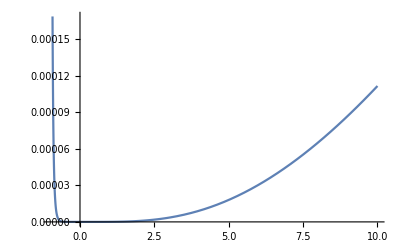

```mathematica
Plot[pfinal[A[lp[k]], B[lm,lp[k],Np]], {k,-0.99,10}]
```